```mathematica
With[
{colors=4},
TableForm[Table[
With[{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors],Range[colors+1,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},
{
n,
a StirlingS2[n-1,colors]-b StirlingS2[n-2,colors]+c StirlingS2[n-3,colors] == StirlingS2[n,colors ]-good,
good,
 StirlingS2[n,colors ]-good
}
],{n,colors,10}
], TableHeadings->{None, {"n","formula","good","bad"}}]
]
```

n | formula | good | bad
4 | True | 1 | 0
5 | a==6 | 4 | 6
6 | 10 a-b==49 | 16 | 49
7 | 65 a-10 b+c==286 | 64 | 286
8 | 350 a-65 b+10 c==1445 | 256 | 1445
9 | 1701 a-350 b+65 c==6746 | 1024 | 6746
10 | 7770 a-1701 b+350 c==30009 | 4096 | 30009

```mathematica
Table[
Labeled[
TableForm[
Table[
With[
{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors+1],Range[colors+2,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},

{
n,
StirlingS2[n,colors ],
StirlingS2[n,colors ]-Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors],{k,0,colors-1}],
StirlingS2[n,colors ]-good,
good
}
]
,{n,colors-1,4}
], TableHeadings->{None, {"n","all","formula","computed bad","computed good"}}]
,
Style[colors,20,Red,Bold]
]
,{colors,2,5}
]
```

{n | all | formula | computed bad | computed good
1 | 0 | 0 | 0 | 0
2 | 1 | 0 | 1 | 0
3 | 3 | 1 | 3 | 0
4 | 7 | 3 | 7 | 02,n | all | formula | computed bad | computed good
2 | 0 | 0 | 0 | 0
3 | 1 | 0 | 1 | 0
4 | 6 | 3 | 6 | 03,n | all | formula | computed bad | computed good
3 | 0 | 0 | 0 | 0
4 | 1 | 0 | 1 | 04,n | all | formula | computed bad | computed good
4 | 0 | 0 | 0 | 05}

```mathematica
Table[
Labeled[
TableForm[
Table[
With[
{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors+1],Range[colors+2,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},

{
n,
StirlingS2[n,colors ],
Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,n-colors],{k,0,colors-1}],
StirlingS2[n,colors ]-good,
good
}
]
,{n,colors,colors+5}
], TableHeadings->{None, {"n","all","formula","computed bad","computed good"}}]
,
Style[colors,20,Red,Bold]
]
,{colors,3,5}
]
```

{n | all | formula | computed bad | computed good
3 | 1 | 0 | 1 | 0
4 | 6 | 0 | 6 | 0
5 | 25 | 0 | 25 | 0
6 | 90 | 27 | 90 | 0
7 | 301 | 175 | 301 | 0
8 | 966 | 660 | 966 | 03,n | all | formula | computed bad | computed good
4 | 1 | 0 | 1 | 0
5 | 10 | 0 | 10 | 0
6 | 65 | 0 | 65 | 0
7 | 350 | 0 | 350 | 0
8 | 1701 | 256 | 1701 | 0
9 | 7770 | 2101 | 7770 | 04,n | all | formula | computed bad | computed good
5 | 1 | 0 | 1 | 0
6 | 15 | 0 | 15 | 0
7 | 140 | 0 | 140 | 0
8 | 1050 | 0 | 1050 | 0
9 | 6951 | 0 | 6951 | 0
10 | 42525 | 3125 | 42525 | 05}

```mathematica
MakeBoxes[StirlingS2[n_,k_],StandardForm]:=RowBox[{"{",GridBox[{{ToString[TraditionalForm[n]]},{ToString[TraditionalForm[k]]}},AutoDelete->False,GridBoxItemSize->{"Columns"->{{Automatic}},"Rows"->{{Automatic}}}],"}"}]
```

```mathematica
StandardForm[Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors}]]
```

∑_(k=0)^colors [colors
colors-k] {n-k
colors-1}

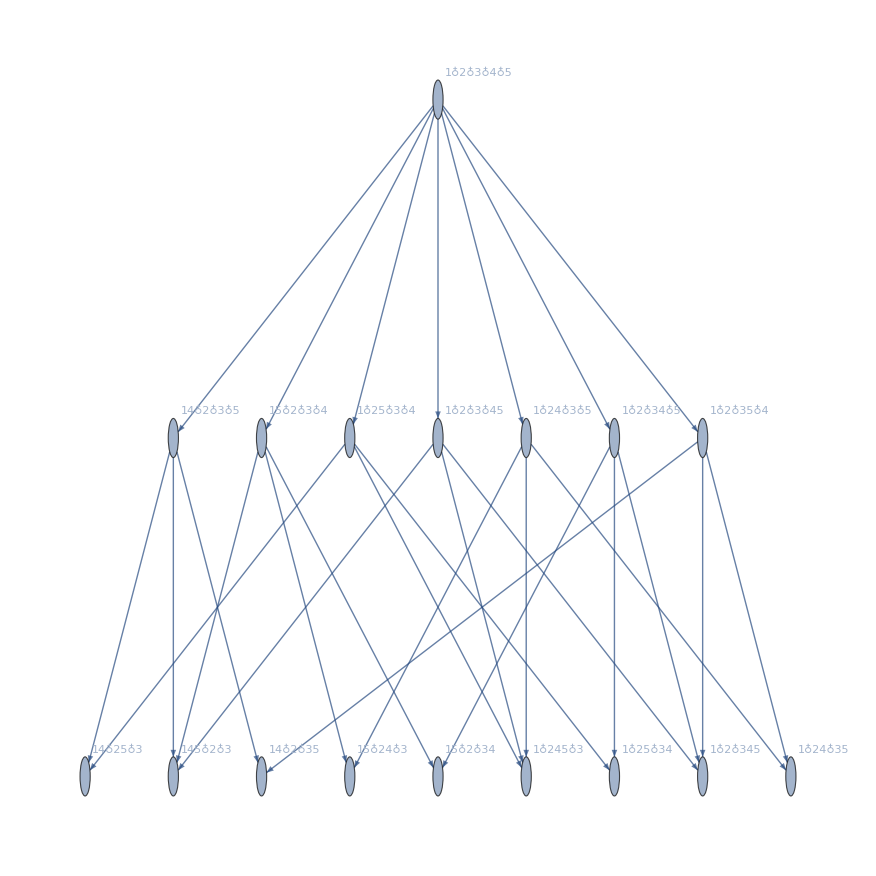

```mathematica
With[
{colors=2,n=5},
FormulaGraph[FindFullFormula[VertexAdd[CompleteGraph[colors+1],Range[colors+2,n]]]]
]
```

```mathematica
With[{colors=4},Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]]
```

-6 {n-3
3}+11 {n-2
3}-6 {n-1
3}+{n
3}

```mathematica
With[{colors=5},Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]]
```

24 {n-4
4}-50 {n-3
4}+35 {n-2
4}-10 {n-1
4}+{n
4}

```mathematica
With[{colors=4},
Table[
Sum[StirlingS1[colors,colors-k]*StirlingS2[n-k,n+1-colors],{k,0,colors-1}],
{n,colors+1,10}]//TableForm
]
```

0
0
64
369
1275
3410

```mathematica
Simplify[Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]]
```

∑_(k=0)^(-1+colors) [colors
colors-k] {n-k
colors-1}

```mathematica
MatrixForm[
Table[
PadRight[Table[
StirlingS2[n,k],{k,0,n}],11]
,{n,0,10}
],
TableHeadings->{Map[Symbol["n"<>ToString[#]]&,Range[0,10]], Map[Symbol["k"<>ToString[#]]&,Range[0,10]]}
]
```

( | k0 | k1 | k2 | k3 | k4 | k5 | k6 | k7 | k8 | k9 | k10
n0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n3 | 0 | 1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n4 | 0 | 1 | 7 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0
n5 | 0 | 1 | 15 | 25 | 10 | 1 | 0 | 0 | 0 | 0 | 0
n6 | 0 | 1 | 31 | 90 | 65 | 15 | 1 | 0 | 0 | 0 | 0
n7 | 0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 | 0 | 0 | 0
n8 | 0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 | 0 | 0
n9 | 0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 0
n10 | 0 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1)

```mathematica
StirlingS2[6,4]
```

65

```mathematica
StirlingS2[5,5+1-4]
```

15

```mathematica
StirlingS2[6,6+1-4]
```

90

```mathematica
Export["D:\\K4.png",MobiusGraph5[K4Key,allGraphs4]]
```

D:\K4.png

```mathematica
Export["D:\\K5.png",Graph[MobiusGraph5[K5Key,allGraphs5],ImageSize->2000],ImageResolution->600]
```

D:\K5.png

```mathematica
Export["D:\\K5.svg",Graph[MobiusGraph5[K5Key,allGraphs5],ImageSize->2000],ImageResolution->600]
```

D:\K5.svg

```mathematica
MobiusGraph6[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],nodeCount=Length[Flatten[allGraphs[key,"vertexsets"]]],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Rotate[Style[SymbolToLabel2[n,nodeCount],40],Pi/6],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Export["D:\\K5.pdf",Graph[MobiusGraph6[K5Key,allGraphs5],ImageSize->2000,AspectRatio->1],ImageResolution->600]
```

D:\K5.pdf

```mathematica
MemoryInUse[]
```

2317981608

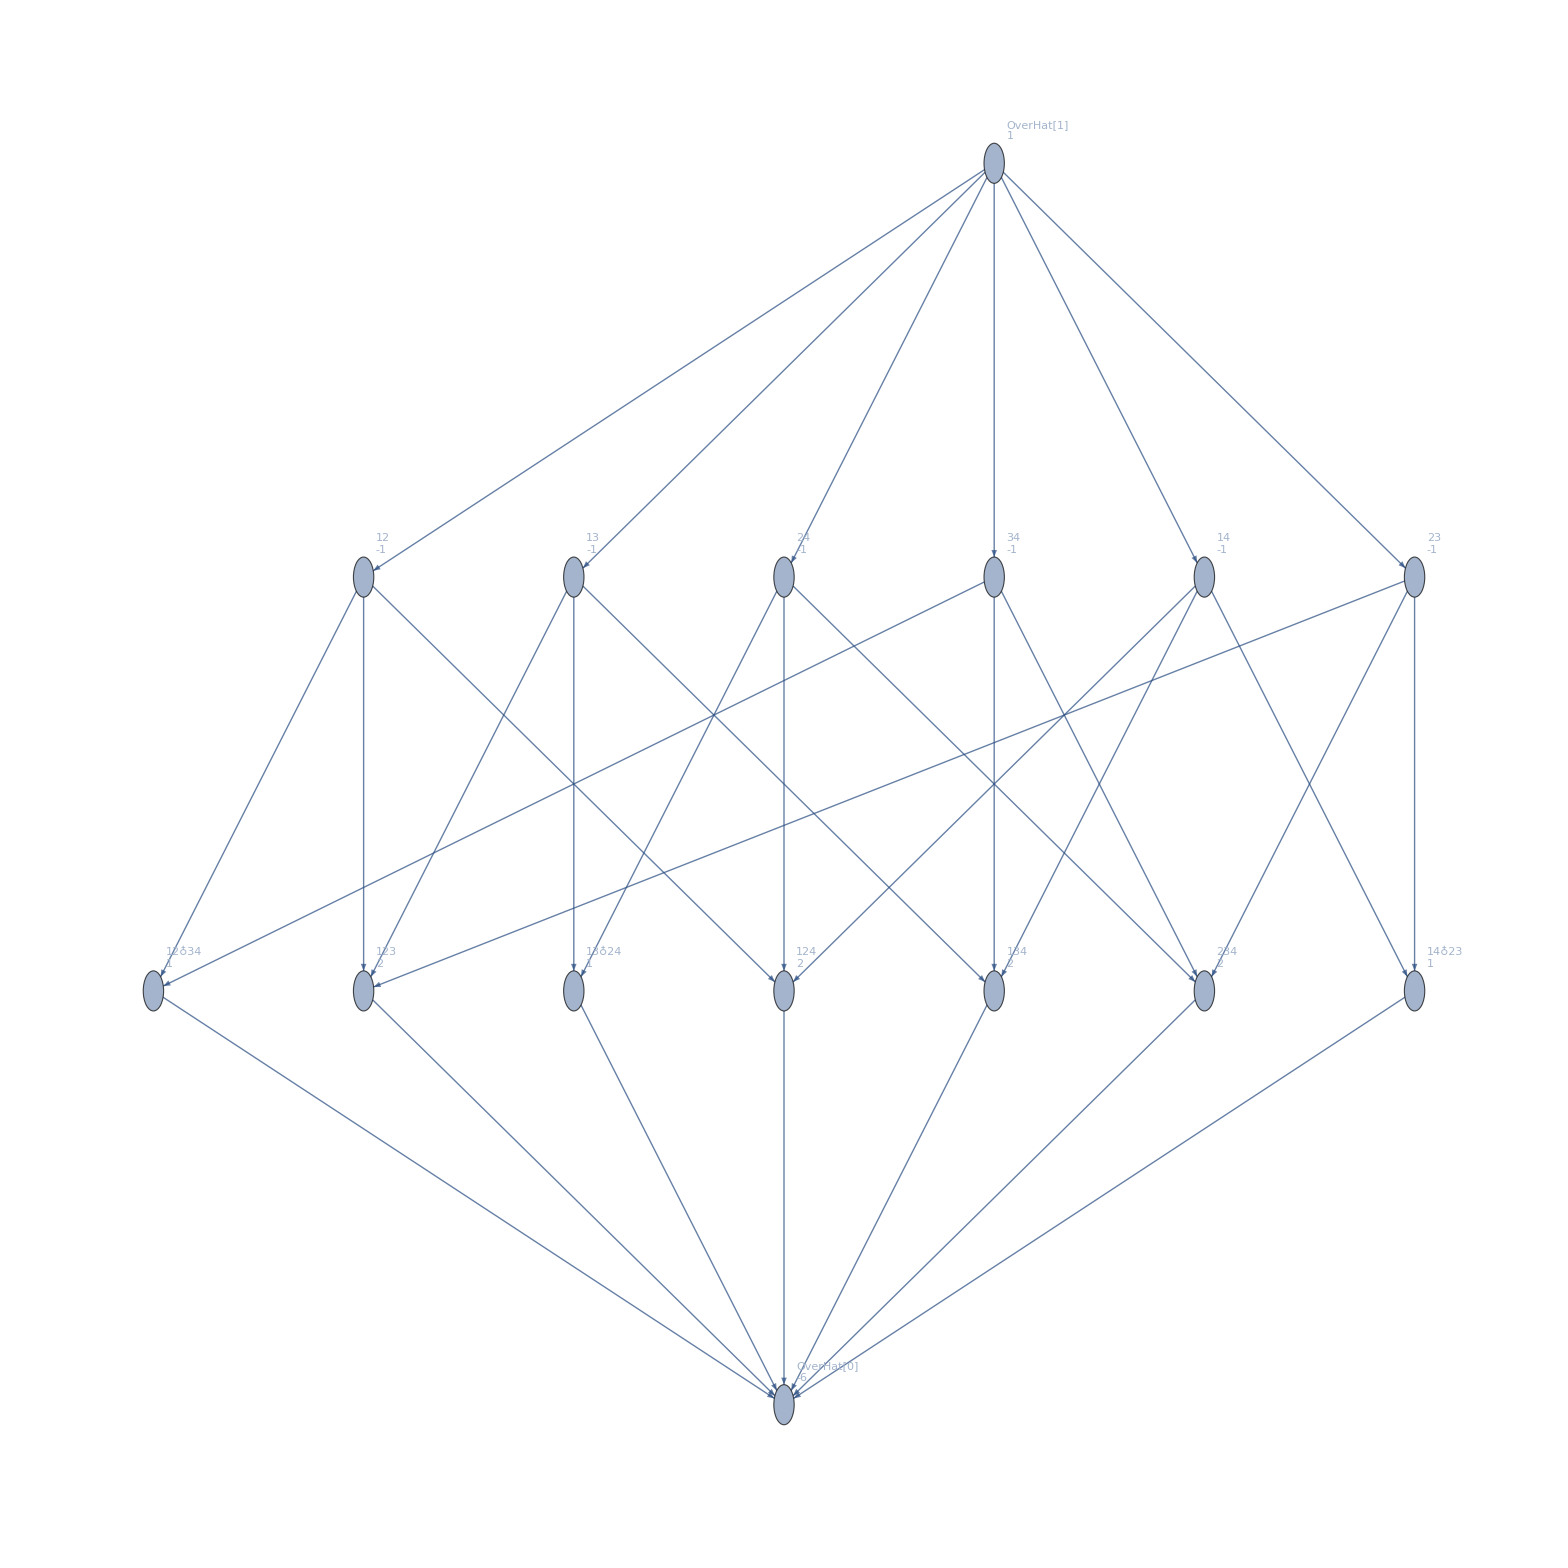

```mathematica
Graph[MobiusGraph5[K4Key,allGraphs4],ImageSize->2000,AspectRatio->1]
```

```mathematica
Export["D:\\K6.pdf",Graph[MobiusGraph5[K6Key,allGraphs6],ImageSize->2000],ImageResolution->600]
```

D:\K6.pdf

```mathematica
$HistoryLength=0
```

0

```mathematica
With[{colors=3},Table[
n-1->{Style[StirlingS2[n,colors-1],Blue],Sum[ Style[StirlingS1[colors,colors-k],Red,20]*Style[StirlingS2[n-k,colors-1],Darker[Green],20],{k,1,colors}]==Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]},{n,colors,10}]
]//TableForm
```

2→{3,0 0+-3 1+0 2==0}
3→{7,0 0+1 2+-3 3==0}
4→{15,0 1+2 3+-3 7==0}
5→{31,0 3+2 7+-3 15==0}
6→{63,0 7+2 15+-3 31==0}
7→{127,0 15+2 31+-3 63==0}
8→{255,0 31+2 63+-3 127==0}
9→{511,0 63+2 127+-3 255==0}

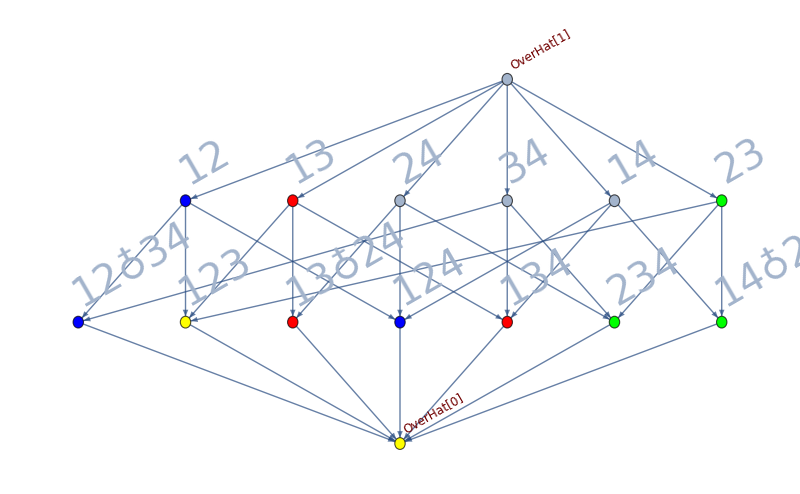

```mathematica
Graph[MobiusGraph6[K4Key,allGraphs4], VertexStyle->Join[Map[#->Blue&,{n12x3x4,n12x34,n124x3}],Map[#->Red&,{n13x2x4,n13x24,n134x2}],Map[#->Green&,{n1x23x4,n1x234,n14x23}],Map[#->Yellow&,{n123x4,n1234}]], ImageSize->800, AspectRatio->1/GoldenRatio]
```

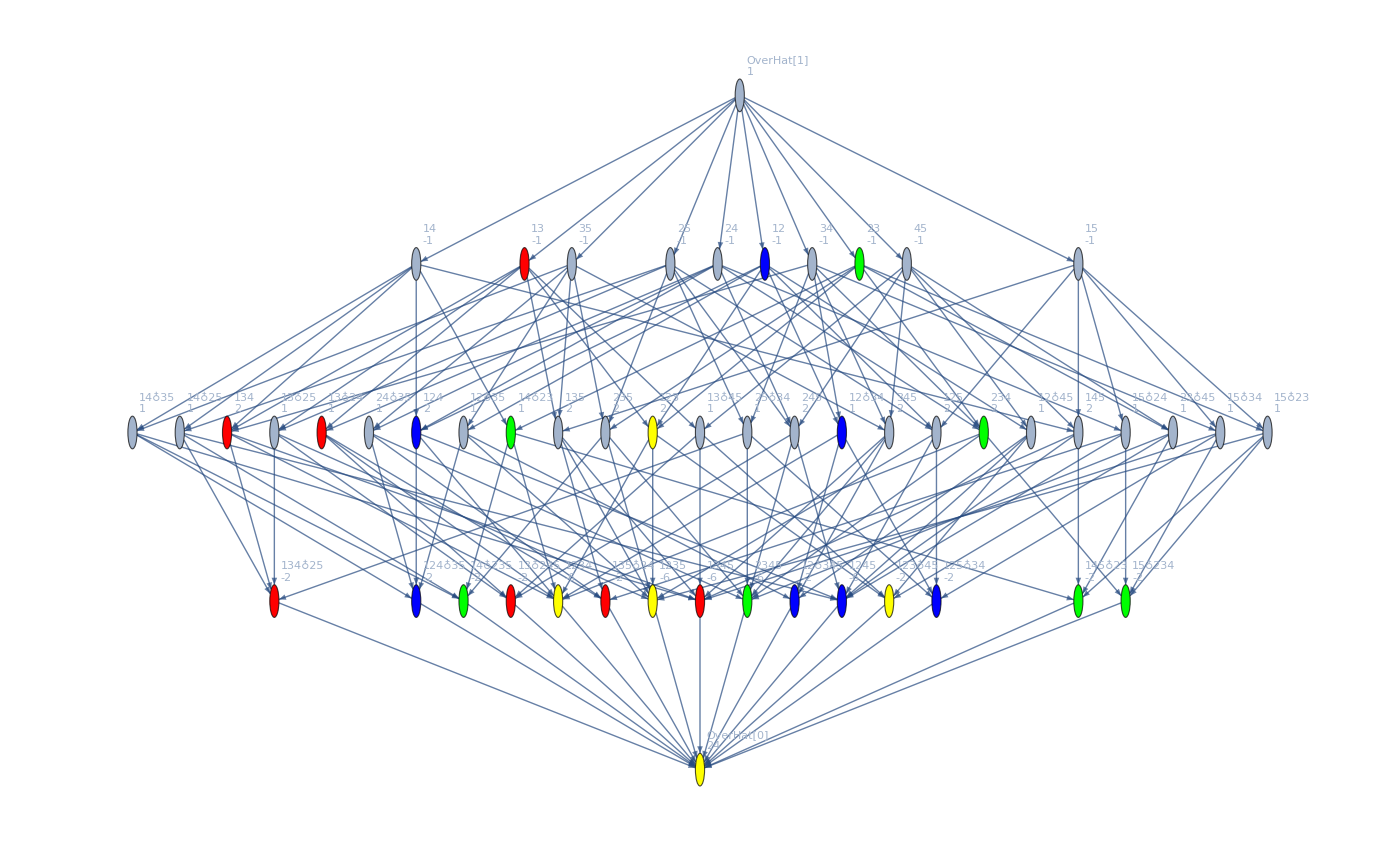

```mathematica
Graph[MobiusGraph5[K5Key,allGraphs5], VertexStyle->Join[Map[#->Blue&,{n12x3x4x5,n12x34x5,n124x3x5,n124x35,n12x345,n1245x3,n125x34}],Map[#->Red&,{n13x2x4x5,n13x24x5,n134x2x5,n134x25,n13x245,n135x24,n1345x2}],Map[#->Green&,{n1x23x4x5,n1x234x5,n14x23x5,n14x235,n145x23,n15x234,n1x2345}],Map[#->Yellow&,{n123x4x5,n1234x5,n1235x4,n123x45,n12345}]], ImageSize->1400, AspectRatio->1/GoldenRatio]
```

```mathematica
StirlingS2[6,4]-(3*StirlingS2[5,3]-2*StirlingS2[4,2])
```

4

```mathematica
StirlingS2[4,2]
```

7

```mathematica
With[{
n=5,
colors=2
},
Table[StandardForm[StirlingS2[Style[n-i,Red],colors]],{i,0,colors}]
]
```

{{5
2},{4
2},{3
2}}

```mathematica
With[{
n=5,
colors=3
},
Table[StandardForm[StirlingS2[n-i,colors-1]],{i,0,colors-1}]
]
```

{15,7,3}

```mathematica
With[{
n=10,
colors=5
},
Table[StirlingS1[colors,colors-i],{i,0,colors-1}].
Table[StirlingS2[n-i,colors-1],{i,0,colors-1}]
]
```

0

```mathematica
With[{
n=5,
colors=2
},
Table[StandardForm[StirlingS2[n-i,colors-1]],{i,0,n-colors}]
]
```

{1,1,1,1}

```mathematica
With[{
n=8,
colors=4
},
Table[StirlingS2[n-i,colors-1],{i,0,colors-1}]
]
```

{966,301,90,25}

```mathematica
3*63-2*31
```

127

```mathematica
Table[StirlingS1[colors,colors-i],{i,0,colors-1}].
Table[StirlingS2[n-i,colors-1],{i,0,colors-1}]//Simplify
```

Table::iterb: Iterator {i,0,-1+colors} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table[[colors
colors-i],{i,0,-1+colors}].Table[{n-i
colors-1},{i,0,-1+colors}]

```mathematica
With[{
n=6,
colors=4
},
TableForm[Table[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],{i,0,colors-1}],TableDepth->1]
]
```

90
-150
66
-6

## the formulas for n nodes

```mathematica
TableForm[
With[{
colors=5
},
Table[
n->Sum[Framed[Labeled[Labeled[StirlingS1[Style[colors,Bold],colors-i],Style[StirlingS1[colors,colors-i],Darker[Green]]]*Labeled[StirlingS2[n-i,Style[colors-1,Bold]],Style[StirlingS2[n-i,colors-1],Darker[Green]]],Style[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],Red]],
FrameStyle->Directive[Thickness[0.1],LightGray]],{i,0,colors-1}]->
Style[Sum[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],{i,0,colors-1}],Green],
{n,colors,15}
]
]
]
```

5→[5
1]24 {1
4}00+[5
2]-50 {2
4}00+[5
3]35 {3
4}00+[5
4]-10 {4
4}1-10+[5
5]1 {5
4}1010→0
6→[5
1]24 {2
4}00+[5
2]-50 {3
4}00+[5
3]35 {4
4}135+[5
4]-10 {5
4}10-100+[5
5]1 {6
4}6565→0
7→[5
1]24 {3
4}00+[5
2]-50 {4
4}1-50+[5
3]35 {5
4}10350+[5
4]-10 {6
4}65-650+[5
5]1 {7
4}350350→0
8→[5
1]24 {4
4}124+[5
2]-50 {5
4}10-500+[5
3]35 {6
4}652275+[5
4]-10 {7
4}350-3500+[5
5]1 {8
4}17011701→0
9→[5
1]24 {5
4}10240+[5
2]-50 {6
4}65-3250+[5
3]35 {7
4}35012250+[5
4]-10 {8
4}1701-17010+[5
5]1 {9
4}77707770→0
10→[5
1]24 {6
4}651560+[5
2]-50 {7
4}350-17500+[5
3]35 {8
4}170159535+[5
4]-10 {9
4}7770-77700+[5
5]1 {10
4}3410534105→0
11→[5
1]24 {7
4}3508400+[5
2]-50 {8
4}1701-85050+[5
3]35 {9
4}7770271950+[5
4]-10 {10
4}34105-341050+[5
5]1 {11
4}145750145750→0
12→[5
1]24 {8
4}170140824+[5
2]-50 {9
4}7770-388500+[5
3]35 {10
4}341051193675+[5
4]-10 {11
4}145750-1457500+[5
5]1 {12
4}611501611501→0
13→[5
1]24 {9
4}7770186480+[5
2]-50 {10
4}34105-1705250+[5
3]35 {11
4}1457505101250+[5
4]-10 {12
4}611501-6115010+[5
5]1 {13
4}25325302532530→0
14→[5
1]24 {10
4}34105818520+[5
2]-50 {11
4}145750-7287500+[5
3]35 {12
4}61150121402535+[5
4]-10 {13
4}2532530-25325300+[5
5]1 {14
4}1039174510391745→0
15→[5
1]24 {11
4}1457503498000+[5
2]-50 {12
4}611501-30575050+[5
3]35 {13
4}253253088638550+[5
4]-10 {14
4}10391745-103917450+[5
5]1 {15
4}4235595042355950→0

```mathematica
TableForm[
Table[With[{
colors=4
},
Sum[Framed[Labeled[Labeled[StirlingS1[Style[colors,Bold],colors-i],Style[StirlingS1[colors,colors-i],Darker[Green]]]*Labeled[StirlingS2[n-i,Style[colors-1,Bold]],Style[StirlingS2[n-i,colors-1],Darker[Green]]],Style[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],Red]],
FrameStyle->Directive[Thickness[0.1],LightGray]],{i,0,colors-1}]->
Style[Sum[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],{i,0,colors-1}],Green]
],
{n,5,10}
]
]
```

[4
1]-6 {2
3}00+[4
2]11 {3
3}111+[4
3]-6 {4
3}6-36+[4
4]1 {5
3}2525→0
[4
1]-6 {3
3}1-6+[4
2]11 {4
3}666+[4
3]-6 {5
3}25-150+[4
4]1 {6
3}9090→0
[4
1]-6 {4
3}6-36+[4
2]11 {5
3}25275+[4
3]-6 {6
3}90-540+[4
4]1 {7
3}301301→0
[4
1]-6 {5
3}25-150+[4
2]11 {6
3}90990+[4
3]-6 {7
3}301-1806+[4
4]1 {8
3}966966→0
[4
1]-6 {6
3}90-540+[4
2]11 {7
3}3013311+[4
3]-6 {8
3}966-5796+[4
4]1 {9
3}30253025→0
[4
1]-6 {7
3}301-1806+[4
2]11 {8
3}96610626+[4
3]-6 {9
3}3025-18150+[4
4]1 {10
3}93309330→0

```mathematica
TableForm[
With[{
colors=3
},
Table[
Sum[Framed[Labeled[Labeled[StirlingS1[Style[colors,Bold],colors-i],Style[StirlingS1[colors,colors-i],Darker[Green]]]*Labeled[StirlingS2[n-i,Style[colors-1,Bold]],Style[StirlingS2[n-i,colors-1],Darker[Green]]],Style[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],Red]],
FrameStyle->Directive[Thickness[0.1],LightGray]],{i,0,colors-1}]->
Style[Sum[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],{i,0,colors-1}],Green],
{n,colors,10}
]
]
]
```

[3
1]2 {1
2}00+[3
2]-3 {2
2}1-3+[3
3]1 {3
2}33→0
[3
1]2 {2
2}12+[3
2]-3 {3
2}3-9+[3
3]1 {4
2}77→0
[3
1]2 {3
2}36+[3
2]-3 {4
2}7-21+[3
3]1 {5
2}1515→0
[3
1]2 {4
2}714+[3
2]-3 {5
2}15-45+[3
3]1 {6
2}3131→0
[3
1]2 {5
2}1530+[3
2]-3 {6
2}31-93+[3
3]1 {7
2}6363→0
[3
1]2 {6
2}3162+[3
2]-3 {7
2}63-189+[3
3]1 {8
2}127127→0
[3
1]2 {7
2}63126+[3
2]-3 {8
2}127-381+[3
3]1 {9
2}255255→0
[3
1]2 {8
2}127254+[3
2]-3 {9
2}255-765+[3
3]1 {10
2}511511→0

```mathematica
TableForm[
With[{
colors=2
},
Table[
Sum[Framed[Labeled[Labeled[StirlingS1[Style[colors,Bold],colors-i],Style[StirlingS1[colors,colors-i],Darker[Green]]]*Labeled[StirlingS2[n-i,Style[colors-1,Bold]],Style[StirlingS2[n-i,colors-1],Darker[Green]]],Style[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],Red]],
FrameStyle->Directive[Thickness[0.1],LightGray]],{i,0,colors-1}]->
Style[Sum[StirlingS1[colors,colors-i]*StirlingS2[n-i,colors-1],{i,0,colors-1}],Green],
{n,colors,10}
]
]
]
```

[2
1]-1 {1
1}1-1+[2
2]1 {2
1}11→0
[2
1]-1 {2
1}1-1+[2
2]1 {3
1}11→0
[2
1]-1 {3
1}1-1+[2
2]1 {4
1}11→0
[2
1]-1 {4
1}1-1+[2
2]1 {5
1}11→0
[2
1]-1 {5
1}1-1+[2
2]1 {6
1}11→0
[2
1]-1 {6
1}1-1+[2
2]1 {7
1}11→0
[2
1]-1 {7
1}1-1+[2
2]1 {8
1}11→0
[2
1]-1 {8
1}1-1+[2
2]1 {9
1}11→0
[2
1]-1 {9
1}1-1+[2
2]1 {10
1}11→0